# User Guide for the MGFtoBeqv Package

This Mathematica notebook is the user guide for the MGFtoBeqv Package.
It explains the main features of the package and gives some useful examples.

The MGFtoBeqv package facilitates the translation from MGFs in their lattice-sum representation to their modular iterated integral representation.

The functions defined in the MGFtoBeqv package are derived from the paper [1].

[1] E. Claasen and M. Doroudiani, From Modular Graph Forms to Modular Iterated Integrals, arXiv:hep-th/2025.abcde.

Copyright © 2025
Emiel Claasen & Mehregan Doroudiani

## Preliminaries

The MGFtoBeqv Package consists of the package file MGFtoBeqv.wl  that uses two other package files ModularGraphForms.m and tetsimplify.wl, as well as several .txt files. For the package to function properly it is important that the MGFtoBeqv.wl package file, the ModularGraphForms.m, the tetsimplify.wl, and all .txt files are placed in the same directory. Furthermore, this user guide must also be placed in the same directory.

We then set Notebook directory as the current directory.

```mathematica
SetDirectory@NotebookDirectory[];
```

## Loading the MGFtoBeqv Package

To load the package we write

```mathematica
Get["MGFtoBeqv.wl"]
```

(****** MGFtoBeqv 1.0 ******)

Authors: Emiel Claasen, Mehregan Doroudiani

Email: emiel.claasen@aei.mpg.de

The MGFtoBeqv package facilitates the conversion of modular graph forms in their lattice-sum representation to their modular iterated integral representation.

(**************************)

Dihedral identity file found at C:\Users\eclaasen\Documents\Wolfram Mathematica\Project Mehregan\Package\DiIds.txt

Trihedral identity file found at C:\Users\eclaasen\Documents\Wolfram Mathematica\Project Mehregan\Package\TriIds.txt

Depth 2 betaeqv constants found at C:\Users\eclaasen\Documents\Wolfram Mathematica\Project Mehregan\Package\betaeqvdepth2const.txt

Depth 3 betaeqv constants found at C:\Users\eclaasen\Documents\Wolfram Mathematica\Project Mehregan\Package\betaeqvdepth3const.txt

Succesfully loaded the MGFtoBeqv package.

## Getting Started

To see all the functions and symbols that the MGFtoBeqv package defines write

```mathematica
Information["MGFtoBeqv`*"]
```

To get information about a specific function either click on the name of the function or write

```mathematica
?FindPrimitive
```

## Conventions

In the literature different conventions have been used to define the lattice-sum representations of modular graph forms. These all come down to different overall powers of  and τ_2, the latter changing the modular weights. As the modular iterated integrals betaeqv transform as anti-holomorphic modular graph forms, it would be most convenient to use the convention in which the MGFs also transform as anti-holomorphic modular forms. However, the package ModularGraphForms.m defines modular graph forms in a different convention without any overall powers of π or τ_2. Instead of having to manually put in the right overall prefactor to suit the convention of betaeqv, we built this into the functions of  MGFtoBeqv.wl so that one can pretend that passing the function c from ModularGraphForms.m into functions of MGFtoBeqv.wl is in the manifestly anti-holomorphic convention. The functions from ModularGraphForms.m like the function c that is used as input in functions from MGFtoBeqv.wl are all explained in [2].

[2] J . Gerken, Basis Decompositions and a Mathematica Package for Modular Graph Forms, J.Phys.A 54 (2021) 19, 195401, arXiv:hep-th/2007.05476

## Conversion of

The functions defined in the package are best explained through an example. Consider the modular graph form , which is defined as

where  and we sum over a 2-dimensional lattice for each . The tree that corresponds to this graph is

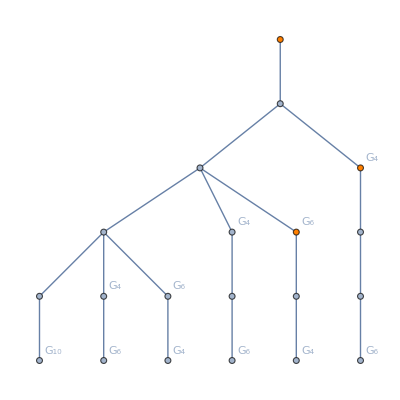

Now to convert the lattice sum to an iterated integral, we would start at the lowest level of the tree and find the primitive of the expressions to go one level up again. In particular, we will focus on the fourth and fifth branch in this example. We have

```mathematica
fourthbranch=-7200 Subscript[τ, 2]^6 Subscript[G, 6] betaeqv[{},{}];
fifthbranch=3600 Subscript[τ, 2]^4 Subscript[G, 4] betaeqv[{},{}];
```

where we attached empty betaeqv functions. We can use the function FindPrimitive to go one level up the tree. This finds the solution to the differential equation

```mathematica
prim1branch4=FindPrimitive[fourthbranch]
prim1branch5=FindPrimitive[fifthbranch ]
```

{450 betaeqv[{4},{6}]}

{900 betaeqv[{2},{4}]}

As a check, we can act with PiNablaBeqv on this and recover the

```mathematica
PiNablaBeqv[prim1branch4]
PiNablaBeqv[prim1branch5]
```

{-7200 G_6 τ_2^6}

{3600 G_4 τ_2^4}

It might be that for given right-hand side of equation (2), there exists no solution within the space of betaeqv. In that case the function returns 0. However, this never happens when dealing with MGFs.

Continuing with the same branches and going one level more up the tree yields

```mathematica
prim2branch4=FindPrimitive[prim1branch4]
prim2branch5=FindPrimitive[prim1branch5]
```

{-1800 betaeqv[{3},{6}]}

{-3600 betaeqv[{1},{4}]}

We now encounter the vertices in the graph with Eisenstein decorations. Therefore we multiply these expressions with the corresponding Eisenstein series and powers of . Furthermore, we see that the vertex at the fifth branch is colored orange, which means that we have a constant to fix by comparing constants of the Laurent polynomials in both representations. From constructing the tree, we know that the modular graph form at this vertex multiplying the G_6 is the non-holomorphic Eisenstein series E_2. We can find the constant of the Laurent polynomial of the MGF using the function CstMGF (which uses CLaurentPoly from ModularGraphForms.m) and the constant of the Laurent polynomial of the betaeqv expansion using CstBetaeqv

```mathematica
CstMGF[c[{{2,0},{2,0}}]]
CstBetaeqv[prim2branch5]
```

0

{0}

As both constants are zero, there is no extra constant to add to the betaeqv expansion to make them match. Therefore, we can continue going another level up the

```mathematica
prim3branch4=FindPrimitive[prim2branch4 Subscript[τ, 2]^4 Subscript[G, 4]]
prim3branch5=FindPrimitive[prim2branch5 Subscript[τ, 2]^6 Subscript[G, 6]]
```

{-450 betaeqv[{3,2},{6,4}]+450 betaeqv[{4,1},{6,4}]}

{225 betaeqv[{1,4},{4,6}]-225 betaeqv[{2,3},{4,6}]}

Going one more step up involves first adding these results and the result from branches on to three as all these branches now merge, after which we use FindPrimitive again. This process has been automated for entire tree in the function MGFtoBeqv

```mathematica
?MGFtoBeqv
```

Applying this function to  yields

```mathematica
MGFtoBeqv[c[{{1,1,1,1,1},{1,1,1,1,1}}]]
```

-16200 betaeqv[{4},{10}]+1800 betaeqv[{1,2},{4,6}]-7200 betaeqv[{2,1},{4,6}]+1800 betaeqv[{2,1},{6,4}]-7200 betaeqv[{3,0},{6,4}]-60 betaeqv[{1},{4}] ζ_3+15 ζ_5

To convert the basis of MGFs at certain graph weights, we can use the function ConvertBasis, which yields a basis of MGFs at those weights in terms of iterated integrals. For example for all MGF at graph weights (5,5) ( belongs to this vector space ), yields

```mathematica
ConvertBasis[5,5]
```

{C[1 | 1 | 3
1 | 1 | 3]→-774 betaeqv[{4},{10}]-120 betaeqv[{2,1},{4,6}]-120 betaeqv[{3,0},{6,4}]-ζ_5/60,(π^5 E_5)/τ_2^5→-630 betaeqv[{4},{10}],C[1 | 0
3 | 0] C[4 | 0
2 | 0]→60 betaeqv[{0,3},{4,6}]+60 betaeqv[{3,0},{6,4}],A[0 | 2 | 3
3 | 0 | 2]→540 betaeqv[{1,2},{4,6}]+360 betaeqv[{2,1},{4,6}]-540 betaeqv[{2,1},{6,4}]-360 betaeqv[{3,0},{6,4}],(π^5 E_2 E_3)/τ_2^5→180 betaeqv[{1,2},{4,6}]+180 betaeqv[{2,1},{6,4}],C[2 | 0
4 | 0] C[3 | 0
1 | 0]→60 betaeqv[{1,2},{6,4}]+60 betaeqv[{2,1},{4,6}],A[0 | 1 | 2 | 2
1 | 1 | 0 | 3]→60 betaeqv[{0,3},{4,6}]-270 betaeqv[{1,2},{4,6}]-60 betaeqv[{1,2},{6,4}]+390 betaeqv[{2,1},{4,6}]+270 betaeqv[{2,1},{6,4}]-390 betaeqv[{3,0},{6,4}]-3 betaeqv[{1},{4}] ζ_3,(π^5 E_2 ζ_3)/τ_2^5→-(6 π^3 betaeqv[{1},{4}] ζ_3)/τ_2^3}

At weights >12 not all constants are known. It is still possible to perform the conversion up to these constants, which are represented by θ_MGF. For example, converting the 6-loop banana graph  gives

```mathematica
MGFtoBeqv[c[{{1,1,1,1,1,1,1},{1,1,1,1,1,1,1}}]]
```

-61916400 betaeqv[{6},{14}]+2041200 betaeqv[{1,4},{4,10}]-16329600 betaeqv[{2,3},{4,10}]+529200 betaeqv[{2,3},{6,8}]-6350400 betaeqv[{3,2},{6,8}]+529200 betaeqv[{3,2},{8,6}]-12700800 betaeqv[{4,1},{6,8}]-6350400 betaeqv[{4,1},{8,6}]+2041200 betaeqv[{4,1},{10,4}]-12700800 betaeqv[{5,0},{8,6}]-16329600 betaeqv[{5,0},{10,4}]-226800 betaeqv[{1,1,2},{4,4,6}]+907200 betaeqv[{1,2,1},{4,4,6}]-226800 betaeqv[{1,2,1},{4,6,4}]+907200 betaeqv[{1,3,0},{4,6,4}]+453600 betaeqv[{2,0,2},{4,4,6}]-2721600 betaeqv[{2,1,1},{4,4,6}]+907200 betaeqv[{2,1,1},{4,6,4}]-226800 betaeqv[{2,1,1},{6,4,4}]-1814400 betaeqv[{2,2,0},{4,4,6}]-4989600 betaeqv[{2,2,0},{4,6,4}]+453600 betaeqv[{2,2,0},{6,4,4}]+907200 betaeqv[{3,0,1},{6,4,4}]-2721600 betaeqv[{3,1,0},{6,4,4}]-1814400 betaeqv[{4,0,0},{6,4,4}]+θ_c[{{1, 1, 1, 1, 1, 1, 1}, {1, 1, 1, 1, 1, 1, 1}}]-17640 betaeqv[{3},{8}] ζ_3+7560 betaeqv[{1,1},{4,4}] ζ_3-15120 betaeqv[{2,0},{4,4}] ζ_3-1890 betaeqv[{1},{4}] ζ_5

Here we encounter an unknown constant θ_("c[{{1, 1, 1, 1, 1, 1, 1}, {1, 1, 1, 1, 1, 1, 1}}]").  The definition of θ_MGF is given by

```mathematica
?θ
```

## Outlook

This concludes the brief introduction to the MGFtoBeqv package. The package can deal with MGFs with <=11 and of at most four vertices. An extension of this package to higher-point MGFs or MGFs of >11 is merely a matter of coding.